```mathematica
Clear[f,x];
f[x_] :=-8;-5<x<-0.3
f[x_] :=-(2/3)x/;0<x<3
f[x_] :=x-5/;3<x<7;
f[x_] :=2;7<x<10

xTicks=Table[n ,{n,0,10}]
yTicks=Table[n,{n,-5,5}]
One=Plot[f[x],{x,0,10.2},PlotRange->{-5.2,5.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.009]}},AxesLabel->{"t","y"}, AspectRatio-> Automatic,GridLines-> {{0,1,2,3,4,5,6,7,8,9,10},{-5,-4,-3, -2,-1,0,1,2,3,4,5}},GridLinesStyle-> Directive[Blue,Dashed]]
To=Graphics[{PointSize[0.025],Point[{0,0}]}];
So=Graphics[{PointSize[0.025],Point[{3,2}]}];
Tu=Graphics[{PointSize[0.025],Point[{-3,-2}]}];
Pe=Graphics[{Thickness[0.004],Circle[{-6,-4},0.14]}];
Po=Graphics[{Thickness[0.004],Circle[{-3,2},0.14]}];
Pu=Graphics[{Thickness[0.004],Circle[{0,3},0.14]}];
Pa=Graphics[{Thickness[0.004],Circle[{0,-3},0.14]}];
Ra=Graphics[{Thickness[0.004],Circle[{3,-2},0.14]}];
Ro=Graphics[{Thickness[0.004],Circle[{6,4},0.14]}];
```

-5<x<-0.3

7<x<10

{0,1,2,3,4,5,6,7,8,9,10}

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

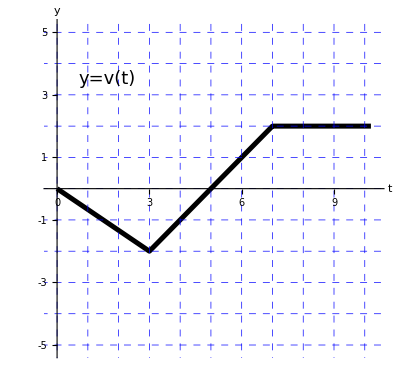

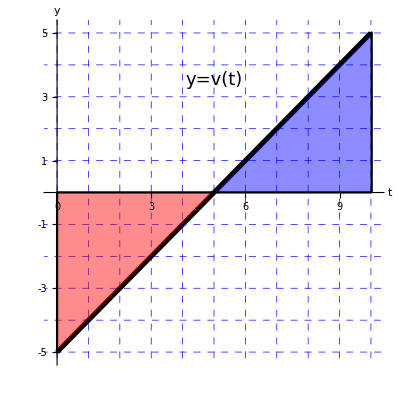

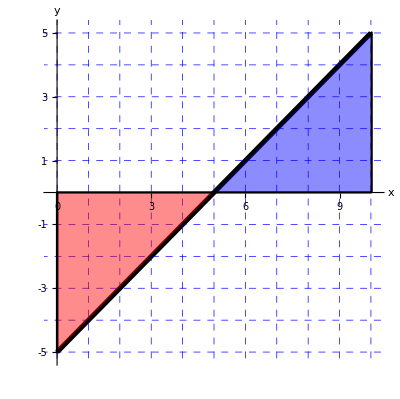

-Graphics-

```mathematica
Clear[f,x];
f[x_] :=-40/;x<0.2
f[x_] :=-4(x-2)/;1<x<2
f[x_] :=5/2(x-2)/;2<x<4
f[x_] :=-40/;4.2<x
xTicks=Table[n ,{n,0,10}]
yTicks=Table[n,{n,-5,5}]
One=Plot[f[x],{x,-0.20,5.4},PlotRange->{-0.2,5.4},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.015]}},AxesLabel->{"t","y"}, AspectRatio-> Automatic,GridLines-> {{0,1,2,3,4,5,6,7,8,9,10},{-5,-4,-3, -2,-1,0,1,2,3,4,5}},GridLinesStyle-> Directive[Blue,Dashed]]
```

{0,1,2,3,4,5,6,7,8,9,10}

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

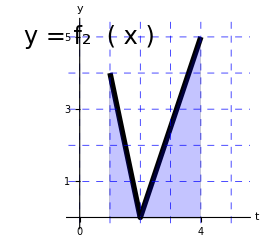

```mathematica
Clear[g,x];
g[x_] :=-30/;x<1;
g[x_] :=8(x-1.5)/;1<x<1.5;
g[x_] :=24(x-1.5)/;1.5<x<2;
g[x_] :=12(3-x)/;2<x<3;
g[x_] :=2(3-x);3<x<4
xTicks=Table[n ,{n,0,10}]
yTicks=Table[4n,{n,-1,4}]
Two=Plot[g[x],{x,0,4},PlotRange->{-4.2,12.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.009]}},AxesLabel->{"t","y"}, GridLines-> {{0,1,2,3,4,5,6,7,8,9,10},{-4,0,4,8,12}},GridLinesStyle-> Directive[Blue,Dashed]]
```

3<x<4

{0,1,2,3,4,5,6,7,8,9,10}

{-4,0,4,8,12,16}

```mathematica
Clear[f,x];
f[x_] :=-40/;x<-1
f[x_] :=-x^2+4 x -3/;2<x<6

f[x_] :=-40/;82.2<x
xTicks=Table[n ,{n,0,8}]
yTicks=Table[n,{n,-20,5}]
One=Plot[f[x],{x,-0.20,6.2},PlotRange->{-15.2,1.4},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.015]}},AxesLabel->{"t","v"}, AspectRatio-> Automatic, Filling-> Axis,GridLines-> {{0,1,2,3,4,5,6,7,8,9,10},{-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3, -2,-1,0,1,2,3,4,5}},GridLinesStyle-> Directive[Blue,Dashed]]
```

{0,1,2,3,4,5,6,7,8}

{-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5}